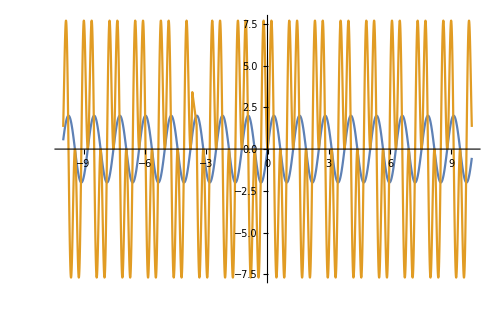
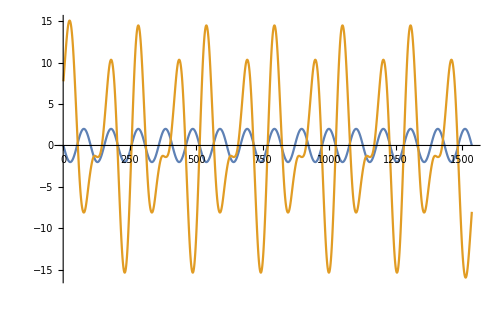

$Aborted

```mathematica
Clear[x];m=.5;

(* Carrier *)
Uc=5;ωc=10;
uc=Uc*Sin[ωc*(#1+#2)]&;
uct=Uc*Sin[11*(#1+#2)]&;
(* Message *)
Um=2;ωm=5;ϕ=0;
um=Um*Sin[ωm*#1+ϕ]&;

(* Amplitude Modulation *)
(*max=MaxValue[um[x],x];*)
(*uam=uc[#1,0]*(1+m*(um[#1])/(max))&;*)
uam=uc[#1,0]*um[#1]&;

(* A de-M *)

cardata=uc[Range[-3Pi,3Pi,Pi/256],20];
cardata2=uct[Range[-3Pi,3Pi,Pi/256],20];
src=um[Range[-3Pi,3Pi,Pi/256]];
data=uam[Range[-3Pi,3Pi,Pi/256]];
lowdata=LowpassFilter[data*cardata2,2,SampleRate->50];
(*dropper=Function[{u,v},tmp=Drop[u,v];tmp=Drop[tmp,-v];Return[tmp];];
{src,data,lowdata}=dropper[#,200]&/@{src,data,lowdata};*)

{Plot[{um[x],uam[x]},{x,-10,10},ImageSize->500],ListLinePlot[{src,lowdata},ImageSize->500]}
(*Periodogram[#,ImageSize->350,PlotRange->All]&/@{src,data,lowdata}*)
```